```mathematica
Clear["Global`*"]
```

QIPmma.m
gsl.m
QIPmma.m

## Testing QIPmma

#### Styling

```mathematica
(* graph styling *)
graphstyle={
	VertexSize->{0.4},
	VertexLabels->{Placed["Name",{1/2*1.05,1/2*1.05}]},
	ImageSize->{146.99479166666538,Automatic},
	VertexStyle->{Directive[EdgeForm[{Thick,Opacity[1],Blue}],Blue]},
	VertexLabelStyle->Directive[White,FontFamily->"IBM Plex Mono",20],
	EdgeStyle->Directive[Black,Thick,Opacity[1]],
	GraphLayout->"CircularEmbedding"
};
```

#### Initial graph definition

```mathematica
Module[{input,out},
	CustomGraph[edges_]:=(

(* edges should be a string*)
(* should be of the form: edges={{1,2},{2,3}} *)
input=Table[edges⟦i,1⟧<->edges⟦i,2⟧
,{i,Length@edges}];

out=Graph[input,graphstyle];
Return[out])
];
```

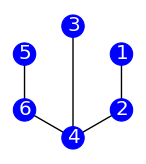

```mathematica
in=CustomGraph[{{1,2},{2,4},{4,3},{4,6},{6,5}}]
```

## Functions

### Dependencies

```mathematica
(* folded Kronecker product *)
Kron:=KroneckerProduct[##]&
```

```mathematica
(* basis states *)
h={{1},{0}};
v={{0},{1}};
d=1/Sqrt[2] (h+v);
a=1/Sqrt[2] (h-v);
r=1/Sqrt[2] (h+I*v);
l=1/Sqrt[2] (h-I*v);
```

```mathematica
(* Partial Trace - adapted from Mark S. Tame, http://library.wolfram.com/infocenter/MathSource/5571/ *)
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr];
TraceSystem[dm_, sys_]:=Block[{Qubits,TrkM,n,M,k,Permut,perm,b,c,p},
Qubits=Reverse[Sort[sys]];(* rearrange the list of qubits to be traced out *)
TrkM=dm;

(* For all qubits to be traced out... *)
For[q=1,q≤Dimensions[Qubits][[1]],q++,
n=Log[2,(Dimensions[TrkM][[1]])]; (* dimensions of original system *)
M=TrkM;
k=Qubits[[q]];

If[k==n,(* if tracing the last system *)
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];(* Pick row p/p+1 and take elements 1/2 through 2^n in steps of 2 - sum thoese and append to zero matrix - do for all rows *)
 ],

For[j=0,j<(n-k),j++,(* if not - permute accordingly *)
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
];
(* and now trace out last system *)
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ]
];

];
Clear[Qubits,n,M,k,Permut,perm,b,c];
TrkM
];
```

### Defined functions

```mathematica
Module[{subGraph,diffGraph,complementGraph,out,g,vertexCoordinates},
	LCQubit[graph_,vertex_]:=(

		(* get the vertex coordinates of the original graph *)
		vertexCoordinates=GraphEmbedding[graph];

		(* apply the vertex coordinates to the original graph *)
		g=Graph[VertexList[graph],EdgeList[graph],VertexCoordinates->vertexCoordinates];

		(* select the subgraph generated by the vertex and its neighbours *)
		subGraph=Subgraph[graph,AdjacencyList[graph,vertex]];

		(* complement the sub graph *)
		complementGraph=GraphComplement[subGraph];

		(* remove the starting subgraph *)
		diffGraph=GraphDifference[graph,subGraph];

		(* union the new subGraph with the remaining main graph *)
		out=GraphUnion[diffGraph,complementGraph];
		out=Graph[out,graphstyle,VertexCoordinates->vertexCoordinates];

	(* return the LC-equivalent graph *)
	Return[out];);
];
```

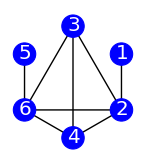

```mathematica
LCQubit[in,4]
```

```mathematica
Module[{perm,prmList,noDuplicates,g,vertexCoordinates,out},
	LCOrbit[graph_]:=(

		(* get the vertex coordinates of the original graph *)
		vertexCoordinates=GraphEmbedding[graph];

		(* apply the vertex coordinates to the original graph *)
		g=Graph[VertexList[graph],EdgeList[graph],VertexCoordinates->vertexCoordinates];

		(* module operations *)
		perm=Permutations[Range[VertexCount[graph]],VertexCount[graph]];
		prmList=FoldList[LCQubit,graph,#]&/@perm//Flatten;
		noDuplicates=DeleteDuplicates[prmList,IsomorphicGraphQ];

		(* ensure styling is correct *)
		out=Graph[noDuplicates,graphstyle,VertexCoordinates->vertexCoordinates];

	(* return the LC-equivalent graph orbit *)
	Return[noDuplicates];)
];
```

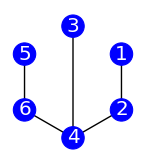
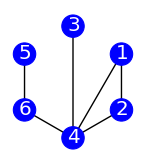
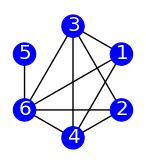
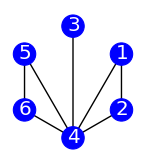
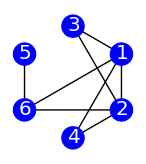
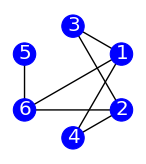
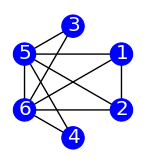
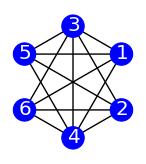
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LCOrbit[in]
```

```mathematica
Module[{vertexCoordinates,g,perm,prmList,noDuplicates,out},
	LCOrbitIsomorphic[graph_]:=(

		(* get the vertex coordinates of the original graph *)
		vertexCoordinates=GraphEmbedding[graph];

		(* apply the vertex coordinates to the original graph *)
		g=Graph[VertexList[graph],EdgeList[graph],VertexCoordinates->vertexCoordinates];

		(* module operations *)
		perm=Permutations[Range[VertexCount[graph]],VertexCount[graph]];
		prmList=FoldList[LCQubit,graph,#]&/@perm//Flatten;
		noDuplicates=Select[prmList,IsomorphicGraphQ[#,graph]&];

		(* ensure styling is correct *)
		out=Graph[noDuplicates,graphstyle,VertexCoordinates->vertexCoordinates];

	(* return the LC-equivalent graph orbit *)
	Return[out];)
];
```

```mathematica
(* above function needs to be fixed *)
(* LCOrbitIsomorphic[g] *)
```

```mathematica
Module[{vertexCoordinates,g,edgeDelete,edgeDeleteGraph,vertexList,vertexDeleted,ordering,out},
	Zmeasurement[graph_,vertex_]:=(

		(* get the vertex coordinates of the original graph *)
		vertexCoordinates=GraphEmbedding[graph];

		(* apply the vertex coordinates to the original graph *)
		g=Graph[VertexList[graph],EdgeList[graph],graphstyle,VertexCoordinates->vertexCoordinates];

		(* module operation *)
		(* finding the complement between all edges and those edges which join to the vertex specified in the function *)
		edgeDelete=Complement[EdgeList[g],EdgeList[g,vertex<->_]];
		edgeDeleteGraph=Graph[edgeDelete];
		vertexList=VertexList[edgeDeleteGraph];

		(* need to work out what edges have been deleted as some vertices will also be removed *)
		(* only showing vertices that still posses an edge *)
		vertexDeleted=Complement[Range@Length@vertexCoordinates,vertexList];
		(* correct re-formatting of variable to parse into the Delete[] function *)
		vertexDeleted={#}&/@vertexDeleted;
		(* new vertex co-ordinates with deleted vertices removed *) 
		vertexCoordinates=Delete[vertexCoordinates,vertexDeleted];

		(* need to get the order correct *)
		(* rearrange the remaining vertexCoordinates with the VertexList[] for the current graph *)
		ordering=Ordering@VertexList[edgeDelete];
		vertexCoordinates=vertexCoordinates⟦#⟧&/@ordering;

		(* ensure styling is correct *)
		out=Graph[edgeDelete,graphstyle,VertexCoordinates->vertexCoordinates];

	Return[out];);
];
```

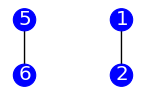

```mathematica
Zmeasurement[in,4]
```

```mathematica
Module[{},
	Ymeasurement[graph_,vertex_]:=(

	(* simply return the Zmeasurement[] function applied to the LC rotated graph *)
	Return[Zmeasurement[LCQubit[graph,vertex],vertex]]);
];
```

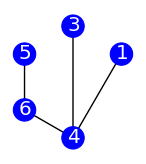

```mathematica
Ymeasurement[in,2]
```

```mathematica
Module[{randomNeighbour,tempGraph,out},
	Xmeasurement[graph_,vertex_]:=(

		(* randomly choose neighbouring vertex (where applicable) *)
		randomNeighbour=RandomChoice@AdjacencyList[graph,vertex];

		(* perform Ymeasurement[] function to said randomly chosen neighbour *)
		tempGraph=Ymeasurement[LCQubit[graph,randomNeighbour],vertex];

		(* correct styling is already applied withing the Ymeasurement[] function *)
		out=LCQubit[tempGraph,randomNeighbour];

	Return[out]);];
```

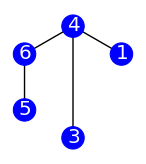

```mathematica
Xmeasurement[in,2]
```

```mathematica
Module[{dim,ops,opsList,coding,codingState,allStates,pos,out,transformations},
	FindStabilzers[state_] := (
	
		(* calculate the dimension of the quantum state *)
		dim=1/Log[Length[state],2];

		(* define a set of Pauli operators *)
		ops=Tuples[Table[{𝕀[i],𝕏[i],ℤ[i],-ℤ[i]},{i,1,dim}]];

		(* List of rules for the application of the Pauli matrices to basis vectors *)
		transformations={
		𝕀[qubit_]->{{H[qubit]->H[qubit],V[qubit]->V[qubit]}},
		𝕏[qubit_]->{{H[qubit]->V[qubit],V[qubit]->H[qubit]}},
		-𝕏[qubit_]->{{H[qubit]->-V[qubit],V[qubit]->-H[qubit]}},
		𝕀*𝕏[qubit_]->{{H[qubit]->𝕀*V[qubit],V[qubit]->𝕀*H[qubit]}},
		-𝕀*𝕏[qubit_]->{{H[qubit]->-𝕀*V[qubit],V[qubit]->-𝕀*H[qubit]}},
		ℤ[qubit_]->{{H[qubit]->H[qubit],V[qubit]->-V[qubit]}},
		-ℤ[qubit_]->{{H[qubit]->-H[qubit],V[qubit]->V[qubit]}},
		𝕀*ℤ[qubit_]->{{H[qubit]->𝕀*H[qubit],V[qubit]->-𝕀*V[qubit]}},
		-𝕀*ℤ[qubit_]->{{H[qubit]->𝕀*H[qubit],V[qubit]->-𝕀*V[qubit]}},
		𝕐[qubit_]->{{H[qubit]->𝕀*V[qubit],V[qubit]->-𝕀*H[qubit]}},
		-𝕐[qubit_]->{{H[qubit]->-𝕀*V[qubit],V[qubit]->𝕀*H[qubit]}},
		𝕀*𝕐[qubit_]->{{H[qubit]->-V[qubit],V[qubit]->H[qubit]}},
		-𝕀*𝕐[qubit_]->{{H[qubit]->V[qubit],V[qubit]->-H[qubit]}}};

		(* flatten the list of Pauli operators *)
		opsList=Flatten[#/.transformations]&/@ops;

		(* define a symbolic coding for the state using Kronecker product *)
		coding=Kron@@Table[{H[i],V[i]},{i,1,dim}]//Flatten;

		(* calculate the symbolic representation of the state *)
		codingState=Total[state*coding];

		(* calculate the symbolic representations of all possible states *)
		allStates=codingState/.#&/@opsList;

		(* find the positions where the state matches each possible state *)
		pos=Position[#==(codingState)&/@allStates,True]//Flatten;

		(* return the symbolic representations of the corresponding Pauli operators *)
		out=ops⟦pos⟧;
	Return[out];)
];
```

```mathematica
state=(1/Sqrt[2])*(Kron[h,h,h]+Kron[v,v,v])
```

{{1/(√2)},{0},{0},{0},{0},{0},{0},{1/(√2)}}

```mathematica
FindStabilzers[state]
```

{{𝕀[1],𝕀[2],𝕀[3]},{𝕀[1],ℤ[2],ℤ[3]},{𝕀[1],-ℤ[2],-ℤ[3]},{𝕏[1],𝕏[2],𝕏[3]},{ℤ[1],𝕀[2],ℤ[3]},{ℤ[1],ℤ[2],𝕀[3]},{-ℤ[1],𝕀[2],-ℤ[3]},{-ℤ[1],-ℤ[2],𝕀[3]}}

```mathematica
Module[{dim,listStab,comb,cliffOp,combCliff,stabComb,graphGen,noSameNodeList,posStab,graphList},
	FindGraph[state_]:=(

		(* compute dimension of the input state *)
		dim=1/Log[Length[state],2];

		(* call function FindSGroupXZSymbolic to get a list of stabilizers from all comb of I,X,Z and -Z*)
		(* As the phase -Z does not matter for finding the graph state, remove it *)
		(* e.g. -Z,I and Z,I stabilize two different states but the same graph state *)
		(* note that the ideal routine would be to find only the stabilizer generators, still open problem *)
		listStab=Union[FindStabilzers[state]/.{-ℤ[qubit_]->ℤ[qubit]}];

		(* consider all combinations of Hadamard and Identity *)
		(* should be enough, but might need to consider phase gate *)
		comb=Tuples[{Table[ℍ[i],{i,dim}],Table[𝕀[i],{i,dim}]}ᵀ];

		(* set the replacement rules *)
		cliffOp={
		ℍ[qubit_]->{𝕀[qubit]->𝕀[qubit],𝕏[qubit]->ℤ[qubit],𝕐[qubit]->𝕐[qubit],ℤ[qubit]->𝕏[qubit]},
		𝕀[qubit_]->{𝕀[qubit]->𝕀[qubit],𝕏[qubit]->𝕏[qubit],𝕐[qubit]->𝕐[qubit],ℤ[qubit]->ℤ[qubit]}};

		(* take the first half of all the comb ;;2^(dim-1) and replace comb with a list of rules *)
		(* the second half is symmetric and will give the same results *)
		combCliff=Flatten[#]&/@(comb[[;;(2^(dim-1))]]/.cliffOp);

		(* apply the rules on the stabilizers *)
		stabComb=listStab/.combCliff;

		(* select only those with one X per group of stabilizers *)
		graphGen=Select[
		Select[#,Count[#,𝕏[_]]==1&]&/@stabComb,
		Length@#>=dim&];

		(* select only those with an X per node *)
		noSameNodeList=Table[
		Count[graphGen[[el]],#]&/@Table[{___,𝕏[i],___},{i,1,dim}],
		{el,Length@graphGen}];

		(* find their positions *)
		posStab=Position[noSameNodeList,Table[1,dim]];

		(* return the list *)
		graphList=graphGen[[#]]&/@posStab;
	Return[Flatten[graphList,1]])
];
```

```mathematica
FindGraph[state]
```

{{{𝕀[1],𝕏[2],ℤ[3]},{ℤ[1],ℤ[2],𝕏[3]},{𝕏[1],𝕀[2],ℤ[3]}},{{𝕀[1],ℤ[2],𝕏[3]},{ℤ[1],𝕏[2],ℤ[3]},{𝕏[1],ℤ[2],𝕀[3]}}}

```mathematica
Module[{linkList,nodeList,toGraph,noDoubleLinks,out},
	DrawGraph[stabList_]:=(

		(* construct list of vertices and edges *)
		linkList=Flatten[#]&/@(Position[#,ℤ[_]]&/@stabList);
		nodeList=Flatten[(Position[#,𝕏[_]]&/@stabList)];

		(* pass the above list through Table[] to construct graph based on mma syntax *)
		toGraph=Table[
		nodeList[[i]]<->#&/@linkList[[i]],
		{i,Length@nodeList}];

		(* remove cases of a repeated edge *)
		noDoubleLinks=DeleteDuplicates[Flatten[toGraph],#1==Reverse[#2]&];

		out=Graph[noDoubleLinks,graphstyle];
	Return[out])
];
```

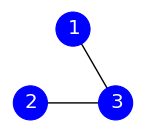
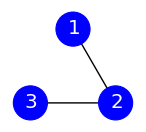

```mathematica
DrawGraph/@FindGraph[state]
```